Navvye Anand, Student Ambassador - Wolfram Research

In this computational essay, we explore the OpenWeatherMap API, and how it can be used for hydrological & Geographical purposes.

## Introduction to OpenWeatherMap

OpenWeatherMap is an online service, owned by OpenWeather Ltd, that provides global weather data via API, including current weather data, forecasts and historical weather data for any geographical location.
Based on a large amount of processing satellite and climate data, it provides satellite imagery, vegetation indices and weather data as well as analytical reports and crop monitoring.

An example of the data taken from the OpenWeatherMap website

## Explaining the API Process

The OpenWeatherMap API uses Polygons to store a unit of Area. We can create polygons either using a POST method, or by manually drawing them onto a map.

#### Creating a Polygon using GeoJSON Coordinates

Start by using your apiKey

```mathematica
apiKey = "3b45dd32459f1d1d846105e225d9cd5c";
```

Create a URL using your apiKey. Allow duplicated = false for no duplicate polygons to be allowed.

```mathematica
url="http://api.agromonitoring.com/agro/1.0/polygons?appid="<> apiKey <> "&duplicated=true";
```

Mention headers and Payload

```mathematica
headers=<|"Content-Type"->"application/json"|>;
payload=<|"name"->"Test","geo_json"-><|"type"->"Feature","properties"-><||>,"geometry"-><|"type"->"Polygon","coordinates"->{{{-122.26514,38.673462},{-122.232127,38.624054},{-122.267076,38.6017},{-122.298185,38.633546},{-122.26514,38.673462}}}|>|>|>;
```

Execute the POST Request

```mathematica
response=URLExecute[HTTPRequest[url,<|"Method"->"POST","Headers"->headers,"Body"->ExportString[payload,"RawJSON"]|>]]
```

{id→65203ca293997d62b1bfbdce,geo_json→{type→Feature,properties→{},geometry→{type→Polygon,coordinates→{{{-122.265,38.6735},{-122.298,38.6335},{-122.267,38.6017},{-122.232,38.6241},{-122.265,38.6735}}}}},name→Test,center→{-122.266,38.6332},area→2303.17,user_id→6519d9be86ec340008b8af3c,created_at→1696611490}

Now, we can verify that the polygon has been created:

```mathematica
viewURL = Last[Import["http://api.agromonitoring.com/agro/1.0/polygons?appid="<> apiKey]]
```

{id→65203ca293997d62b1bfbdce,geo_json→{type→Feature,properties→{},geometry→{type→Polygon,coordinates→{{{-122.265,38.6735},{-122.298,38.6335},{-122.267,38.6017},{-122.232,38.6241},{-122.265,38.6735}}}}},name→Test,center→{-122.266,38.6332},area→2303.17,user_id→6519d9be86ec340008b8af3c,created_at→1696611490}

## Importing & Visualizing Data

Importing the Data using the API is a two step process. We must first call the polygons ID API, and then use that to get Satellite, NDVI and other data in the JSON format. After that, we can process the data and look at some applications

```mathematica
urlToFetch = Import["https://api.agromonitoring.com/agro/1.0/image/search?start=1646245800&end=1646850600&polyid=651f1602287b0e3c2bfcebe8&appid=3b45dd32459f1d1d846105e225d9cd5c"]
```

{{dt→1646438400,type→Sentinel-2,dc→100,cl→100,sun→{elevation→42.46,azimuth→151.269},image→{truecolor→http://api.agromonitoring.com/image/1.0/1006222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/1106222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/1206222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/1306222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/1406222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/1506222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/1606222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/1706222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1006222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1106222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1206222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1306222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1406222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1506222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1606222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1706222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/1236222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/1336222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/1436222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/1536222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/1636222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/1736222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/1016222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/1116222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/1226222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/1326222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/1426222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/1526222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/1626222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/1726222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c}},{dt→1646697600,type→Landsat 8,dc→100,cl→0,sun→{elevation→42.6017,azimuth→147.631},image→{truecolor→http://api.agromonitoring.com/image/1.0/00062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/01062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/02062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/03062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/04062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/05062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/06062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/07062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/00062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/01062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/02062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/03062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/04062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/05062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/06062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/07062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/02362269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/03362269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/04362269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/05362269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/06362269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/07362269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/00162269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/01162269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/02262269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/03262269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/04262269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/05262269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/06262269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/07262269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c}}}

Let's break down the URL
1) image - to get the image data values 
2) start  = EPOCH Time Start Value
3) end = EPOCH Time End Value 
4) polyID = PolygonID - can be found easily by visiting the website, or by looking at the metadata if you created the polygon using an API Request

5) appID = APIKEY

```mathematica
Flatten[Table[Values[Values[urlToFetch[[i]][[6]]]], {i, Length[urlToFetch]}]]
```

{http://api.agromonitoring.com/image/1.0/1006222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1106222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1206222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1306222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1406222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1506222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1606222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1706222a800/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/00062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/01062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/02062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/03062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/04062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/05062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/06062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/07062269c80/651f1602287b0e3c2bfcebe8?appid=3b45dd32459f1d1d846105e225d9cd5c}

```mathematica
Import/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Import["https://api.agromonitoring.com/agro/1.0/image/search?start=1646245800&end=1646850600&polyid=651eb60393997d383cbfbdb9&appid=3b45dd32459f1d1d846105e225d9cd5c"]
```

{{dt→1646265600,type→Sentinel-2,dc→100,cl→100,sun→{elevation→38.121,azimuth→151.75},image→{truecolor→http://api.agromonitoring.com/image/1.0/10062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/11062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/12062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/13062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/14062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/15062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/16062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/17062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/10062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/11062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/12062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/13062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/14062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/15062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/16062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/17062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/12362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/13362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/14362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/15362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/16362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/17362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/10162200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/11162200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/12262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/13262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/14262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/15262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/16262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/17262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}},{dt→1646524800,type→Landsat 8,dc→100,cl→100,sun→{elevation→39.6209,azimuth→150.041},image→{truecolor→http://api.agromonitoring.com/image/1.0/0006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/0106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/0206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/0306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/0406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/0506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/0606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/0706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/0236223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/0336223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/0436223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/0536223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/0636223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/0736223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/0016223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/0116223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/0226223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/0326223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/0426223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/0526223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/0626223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/0726223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}},{dt→1646524800,type→Sentinel-2,dc→100,cl→100,sun→{elevation→40.037,azimuth→154.234},image→{truecolor→http://api.agromonitoring.com/image/1.0/1006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/1106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/1206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/1306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/1406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/1506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/1606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/1706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/1236223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/1336223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/1436223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/1536223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/1636223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/1736223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/1016223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/1116223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/1226223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/1326223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/1426223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/1526223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/1626223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/1726223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}},{dt→1646697600,type→Sentinel-2,dc→100,cl→100,sun→{elevation→40.08,azimuth→151.346},image→{truecolor→http://api.agromonitoring.com/image/1.0/10062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/11062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/12062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/13062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/14062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/15062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/16062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/17062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/10062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/11062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/12062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/13062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/14062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/15062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/16062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/17062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/12362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/13362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/14362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/15362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/16362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/17362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/10162269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/11162269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/12262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/13262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/14262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/15262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/16262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/17262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}}}

```mathematica
Flatten[Table[Values[Values[%[[i]][[6]]]], {i, Length@%}]]
```

{http://api.agromonitoring.com/image/1.0/10062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/11062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/12062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/13062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/14062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/15062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/16062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/17062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/0706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/1706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/10062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/11062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/12062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/13062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/14062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/15062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/16062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/image/1.0/17062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}

```mathematica
Import/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Calculating Change in Water Levels

We choose the satellite images of blue color

```mathematica
img1 = -Graphics-;
img2 = -Graphics-;
```

```mathematica
SameQ[img1, img2]
```

False

The images are not the same, hence we know that there has been a change in the water levels

```mathematica
Binarize[ColorNegate@Image[img1]]
```

-Graphics-

```mathematica
Binarize[ColorNegate@Image[img2]]
```

-Graphics-

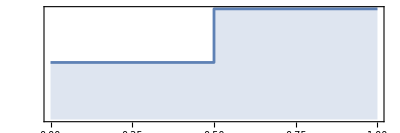
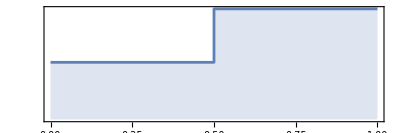

```mathematica
ImageHistogram/@{-Graphics-, -Graphics-}
```

The graphs appear similar, indicating that not a lot of change has taken place in the time period. We can find the change in the area

```mathematica
Last/@ImageLevels[-Graphics-]
```

{32038,62138}

```mathematica
Ratio1 = 100*N[Last[%]/(Last[%] + First[%])]
```

65.9807

Around 65.9807% of the region is covered by water in Image1

```mathematica
Last/@ImageLevels[-Graphics-]
```

{32085,62091}

```mathematica
Ratio2 = 100*N[Last[%]/(Last[%] + First[%])]
```

65.9308

Around 65.9308% of the region is covered by water in Image1

```mathematica
DifferenceInWaterLevels = (Ratio1 - Ratio2)
```

0.0499066

And hence we calculate the change in water % to be around 0.04%

## Using Statistics and NDVI data

We can also calculate some important Statistics and use the NDVI Data

#### JSONData

```mathematica
%103
```

{{dt→1646265600,type→Sentinel-2,dc→100,cl→100,sun→{elevation→38.121,azimuth→151.75},image→{truecolor→http://api.agromonitoring.com/image/1.0/10062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/11062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/12062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/13062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/14062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/15062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/16062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/17062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/10062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/11062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/12062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/13062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/14062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/15062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/16062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/17062200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/12362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/13362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/14362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/15362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/16362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/17362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/10162200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/11162200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/12262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/13262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/14262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/15262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/16262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/17262200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}},{dt→1646524800,type→Landsat 8,dc→100,cl→100,sun→{elevation→39.6209,azimuth→150.041},image→{truecolor→http://api.agromonitoring.com/image/1.0/0006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/0106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/0206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/0306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/0406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/0506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/0606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/0706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/0706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/0236223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/0336223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/0436223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/0536223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/0636223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/0736223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/0016223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/0116223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/0226223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/0326223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/0426223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/0526223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/0626223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/0726223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}},{dt→1646524800,type→Sentinel-2,dc→100,cl→100,sun→{elevation→40.037,azimuth→154.234},image→{truecolor→http://api.agromonitoring.com/image/1.0/1006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/1106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/1206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/1306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/1406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/1506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/1606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/1706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1006223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1106223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1206223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1306223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1406223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1506223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1606223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/1706223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/1236223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/1336223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/1436223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/1536223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/1636223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/1736223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/1016223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/1116223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/1226223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/1326223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/1426223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/1526223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/1626223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/1726223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}},{dt→1646697600,type→Sentinel-2,dc→100,cl→100,sun→{elevation→40.08,azimuth→151.346},image→{truecolor→http://api.agromonitoring.com/image/1.0/10062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/image/1.0/11062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/image/1.0/12062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/image/1.0/13062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/image/1.0/14062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/image/1.0/15062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/image/1.0/16062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/image/1.0/17062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},tile→{truecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/10062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/11062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/12062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/13062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/14062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/15062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/16062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/tile/1.0/{z}/{x}/{y}/17062269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},stats→{ndvi→http://api.agromonitoring.com/stats/1.0/12362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/stats/1.0/13362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/stats/1.0/14362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/stats/1.0/15362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/stats/1.0/16362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/stats/1.0/17362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c},data→{truecolor→http://api.agromonitoring.com/data/1.0/10162269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,falsecolor→http://api.agromonitoring.com/data/1.0/11162269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndvi→http://api.agromonitoring.com/data/1.0/12262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi→http://api.agromonitoring.com/data/1.0/13262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,evi2→http://api.agromonitoring.com/data/1.0/14262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,nri→http://api.agromonitoring.com/data/1.0/15262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,dswi→http://api.agromonitoring.com/data/1.0/16262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,ndwi→http://api.agromonitoring.com/data/1.0/17262269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}}}

#### Visualizing Statistical Values

```mathematica
Flatten[Values[Values[Table[KeyTake[%103[[i]],"stats" ], {i, 1,Length[%103]}]]]]
```

{http://api.agromonitoring.com/stats/1.0/12362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/13362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/14362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/15362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/16362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/17362200500/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/0236223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/0336223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/0436223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/0536223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/0636223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/0736223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/1236223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/1336223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/1436223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/1536223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/1636223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/1736223f980/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/12362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/13362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/14362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/15362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/16362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c,http://api.agromonitoring.com/stats/1.0/17362269c80/651eb60393997d383cbfbdb9?appid=3b45dd32459f1d1d846105e225d9cd5c}

```mathematica
Import/@%
```

{{std→0.227591,p25→-0.460317,num→62166,min→-0.487836,max→0.469155,median→-0.447853,p75→-0.416415,mean→-0.347096},{std→0.10881,p25→-0.155093,num→62166,min→-0.173809,max→0.511349,median→-0.151857,p75→-0.14804,mean→-0.108149},{std→0.0635181,p25→-0.0819834,num→62166,min→-0.0965492,max→0.351561,median→-0.0794587,p75→-0.0775237,mean→-0.0553845},{std→0.395479,p25→-0.889368,num→15538,min→-0.929339,max→0.546385,median→-0.866667,p75→-0.807435,mean→-0.682805},{std→0.24619,p25→1.50408,num→15538,min→0.68595,max→1.70084,median→1.59505,p75→1.63607,mean→1.48523},{std→0.285947,p25→0.582177,num→15538,min→-0.269729,max→0.828947,median→0.682657,p75→0.728395,mean→0.55556},{std→0.000647498,p25→0.0149723,num→15538,min→0.0132992,max→0.0173064,median→0.0154464,p75→0.0158616,mean→0.0153919},{std→0.0106006,p25→0.137574,num→15538,min→0.114023,max→0.179384,median→0.145881,p75→0.153061,mean→0.145277},{std→0.000783305,p25→0.0161933,num→15538,min→0.0142691,max→0.0189366,median→0.0167965,p75→0.0173038,mean→0.0167223},{std→0.0175518,p25→-0.544291,num→15538,min→-0.572735,max→-0.490263,median→-0.526526,p75→-0.513854,mean→-0.529013},{std→0.0171807,p25→1.51402,num→15538,min→1.49055,max→1.57167,median→1.52657,p75→1.54387,mean→1.52891},{std→0.0169903,p25→0.525388,num→15538,min→0.501982,max→0.582581,median→0.537549,p75→0.554871,mean→0.540011},{std→0.00324076,p25→-0.0022484,num→62166,min→-0.0114391,max→0.0113432,median→-0.000281452,p75→0.00224256,mean→0.0000147974},{std→0.0277798,p25→-0.0176884,num→62166,min→-0.0837256,max→0.118621,median→-0.00230185,p75→0.0194994,mean→0.00198444},{std→0.00374153,p25→-0.002586,num→62166,min→-0.0131257,max→0.0132379,median→-0.000324361,p75→0.00259595,mean→0.0000316969},{std→0.0314761,p25→-0.418716,num→15538,min→-0.451732,max→-0.336808,median→-0.39782,p75→-0.361501,mean→-0.391689},{std→0.0314871,p25→1.31823,num→15538,min→1.28055,max→1.42189,median→1.3551,p75→1.37398,mean→1.34745},{std→0.031439,p25→0.361496,num→15538,min→0.333043,max→0.454905,median→0.399628,p75→0.418869,mean→0.391706},{std→0.188353,p25→-0.362295,num→62166,min→-0.393993,max→0.463884,median→-0.341118,p75→-0.308396,mean→-0.261235},{std→0.106789,p25→-0.156206,num→62166,min→-0.166401,max→0.494869,median→-0.152364,p75→-0.142448,mean→-0.106426},{std→0.0632401,p25→-0.087435,num→62166,min→-0.0936382,max→0.337637,median→-0.084957,p75→-0.0791283,mean→-0.0583404},{std→0.312786,p25→-0.681956,num→15538,min→-0.734628,max→0.494711,median→-0.645065,p75→-0.581839,mean→-0.50894},{std→0.148879,p25→1.30657,num→15538,min→0.717048,max→1.43508,median→1.34717,p75→1.36797,mean→1.28426},{std→0.171098,p25→0.325228,num→15538,min→-0.239022,max→0.51227,median→0.388795,p75→0.432485,mean→0.322656}}

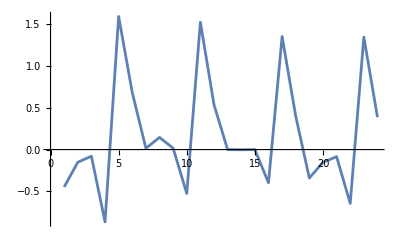

```mathematica
ListLinePlot["median"/.%142]
```

The median value of the index

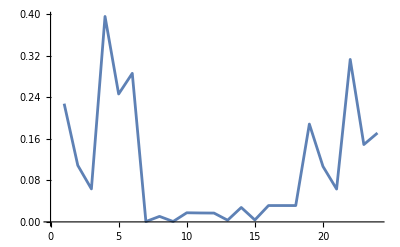

```mathematica
ListLinePlot["std"/.%142]
```

The standard deviation of the index

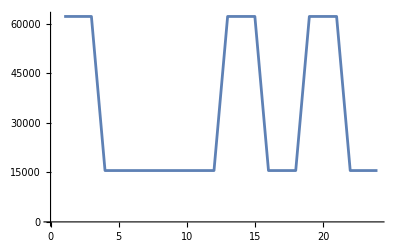

```mathematica
ListLinePlot["num"/.%142]
```

Number of pixels in the image

#### Using NDVI Data

```mathematica
Import/@Values[Flatten["data"/.%103]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Sun Data

```mathematica
sunData = "sun"/.%103
```

{{elevation→38.121,azimuth→151.75},{elevation→39.6209,azimuth→150.041},{elevation→40.037,azimuth→154.234},{elevation→40.08,azimuth→151.346}}

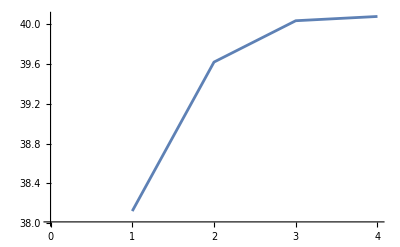

```mathematica
ListLinePlot["elevation"/.sunData]
```

Elevation of the Sun

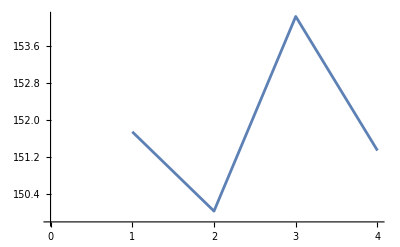

```mathematica
ListLinePlot["azimuth"/.sunData]
```

Azimuth Values of the Sun

## Bonus: Plotting the Flight of the Satellites

```mathematica
satelliteName = RandomChoice["type"/.%103]
```

Landsat 8

```mathematica
With[{data = EntityValue[SemanticInterpretation@satelliteName
, {"Position", "PositionLine"}]},
 GeoGraphics[{Gray, Thickness[.005], 
   Arrowheads[{{0.05, 0.4}, {0.05, 0.13}}], Arrow @@ data[[2]], Red, 
   PointSize[.01], Point[data[[1]]], Opacity[.1], Black, 
   GeoVisibleRegion[data[[1]]]}, GeoCenter -> data[[1]], 
  GeoRange -> "World"]]
```

-Graphics-

## Bonus : Dynamic Image Comparison

```mathematica
img1 = -Graphics-;
```

```mathematica
img2 =-Graphics-;
```

```mathematica
Module[{x,y,s},Row[{DynamicImage[img1,ZoomCenter->Dynamic[Scaled[{x,y}]],ZoomFactor->Dynamic[s],AppearanceElements->{"Pan","Scrollbars","ZoomButtons","Zoom"},ImageSize->{240,360}],DynamicImage[img2,ZoomCenter->Dynamic[Scaled[{x,y}]],ZoomFactor->Dynamic[s],AppearanceElements->{"Pan","Scrollbars","ZoomButtons","Zoom"},ImageSize->{240,360}]}]]
```

## Conclusion

The lack of real time satellite data in the Wolfram Language has been combatted by using this API. I would like to thank the people on Wolfram Community for inspiring this project - especially Professor M.A.Ghorbani and Erfan Abdi.  We can use the NDVI data for calculating the green score of a place.